### Exercici 1

Calculeu la probabilitat que al tirar 7 cops daus surti un 5 com a mínim.

```mathematica
N[1-(5/6)^7]
```

0.720918

Simuleu 1000 tirades de 7 daus i compteu la freqüència de que surti al menys un 5.

```mathematica
simular[r_Integer,n_Integer] := Table[Random[Integer,{1,r}],{i,n}]
```

```mathematica
numeroTirades[n_Integer,o_Integer,b_Integer] := Table[simular[o,b],{i,1,n}]
```

```mathematica
numeroTirades[1000,6,7];
```

```mathematica
contarNumero[i_Integer] := N[Length[Select[numeroTirades[1000,6,7],MemberQ[#,i]&]]/1000]
```

```mathematica
contarNumero[5]
```

0.721

Compareu els dos resultats.

```mathematica
N[1-(5/6)^7]
```

0.720918

```mathematica
contarNumero[5]
```

0.719

### Exercici 2

Carregeu el paquet

```mathematica
<<Combinatorica`
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionaliy. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

Doneu la llista d' arestes del graf següent:

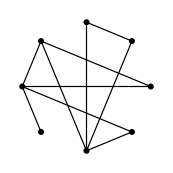

{{1,2},{1,6},{2,6},{3,4},{3,6},{3,8},{4,5},{4,7},{4,8},{7,6}}

⁃Graph:<10,8,Undirected>⁃

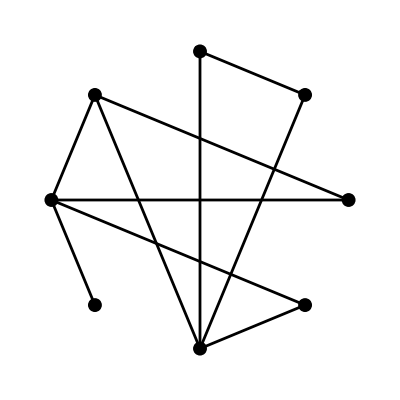

```mathematica
Ar={{1,2},{1,6},{2,6},{3,4},{3,6},{3,8},{4,5},{4,7},{4,8},{7,6}}
G=FromUnorderedPairs[Ar]
ShowLabeledGraph[G]
```

```mathematica
Edges[G]
```

{{1,2},{1,6},{2,6},{3,4},{3,6},{3,8},{4,5},{4,7},{4,8},{6,7}}

Calculeu el diametre, radi i excentricitat del graf.

```mathematica
Diameter[G]
```

4

```mathematica
Radius[G]
```

2

```mathematica
Eccentricity[G]
```

{4,4,2,3,4,3,2,3}